```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsOld=ReadList[FileNameJoin[{Directory[],"files/SortetBasisFull.txt"}]];
PureIntegralsNew=PureIntegralsOld;
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
PureIntegralsOld[[145]]=PureIntegralsOld[[145]]/.root[x_^2]:>x
$P=2^31-1;
```

-2 (-ep^3+2 ep^4) (mt2 s12-mt2 s123+s123 s345-s12 s45) hxb[0,1,0,1,1,1,0,1,1,0,0,0,0]

# Assemble basis

```mathematica
SelectInts={7,8,18,19,75,78,79,80,86,87,88,112,115,158,159,160,161,162,163}

PureIntegralsNew=PureIntegralsOld;

PureIntegralsNew[[158]]=ep^4 hxb[1,0,1,1,0,0,1,1,0,0,0,0,0];
PureIntegralsNew[[159]]=ep^3 hxb[1,0,1,1,0,0,1,1,0,0,0,0,0]/PR[4]
PureIntegralsNew[[160]]=ep^3 hxb[1,0,1,1,0,0,1,1,0,0,0,0,0]/PR[1];
PureIntegralsNew[[161]]=ep^3 hxb[1,0,1,1,0,0,1,1,0,0,0,0,0]/PR[3];
PureIntegralsNew[[162]]=ep^3 hxb[1,0,1,1,0,0,1,1,0,0,0,0,0](1/PR[7])//Expand;
PureIntegralsNew[[163]]=ep^3 hxb[1,0,1,1,0,0,1,1,0,0,0,0,0](1/PR[8])//Expand;


(*PureIntegralsNew[[162]]=PureIntegralsOld[[162]]+PureIntegralsOld[[163]]
PureIntegralsNew[[163]]=PureIntegralsOld[[162]]-PureIntegralsOld[[163]]*)

SubPureInts=PureIntegralsNew[[SelectInts]];

Newsqrts=(Cases[SubPureInts,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsOld,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];

Export[FileNameJoin[{NotebookDirectory[],"SubBasis.txt"}],SubPureInts];
```

{7,8,18,19,75,78,79,80,86,87,88,112,115,158,159,160,161,162,163}

ep^3 hxb[1,0,1,2,0,0,1,1,0,0,0,0,0]

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 mt2 s12+(-mt2-s12+s345)^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s56+s56^2}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)}

```mathematica
PureIntegralsNew[[158]]
PureIntegralsNew[[159]]
PureIntegralsNew[[160]]
PureIntegralsNew[[161]]
PureIntegralsNew[[162]]
PureIntegralsNew[[163]]
```

ep^4 hxb[1,0,1,1,0,0,1,1,0,0,0,0,0]

ep^3 hxb[2,0,1,1,0,0,1,1,0,0,0,0,0]

ep^3 hxb[1,0,2,1,0,0,1,1,0,0,0,0,0]

ep^3 hxb[1,0,1,2,0,0,1,1,0,0,0,0,0]

ep^3 hxb[1,0,1,1,0,0,2,1,0,0,0,0,0]

ep^3 hxb[1,0,1,1,0,0,1,2,0,0,0,0,0]

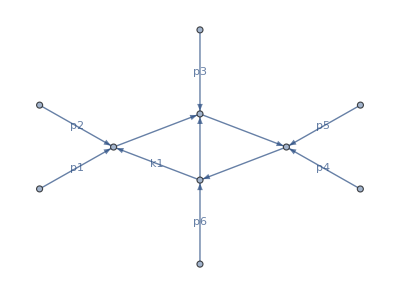

```mathematica
plotDiagram[hxb[1,0,1,1,0,1,0,2,0,0,0,0,0]]
```

```mathematica
mt2^2-2 mt2 s123+s123^2-2 mt2 s345+2 s123 s345+s345^2-4 s12 s45//FullSimplify
```

(-mt2+s123+s345)^2-4 s12 s45

```mathematica
(mt2 s12-mt2 s123+s123 s345-s12 s45)^2//Expand
```

mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45-2 s12 s123 s345 s45+s12^2 s45^2

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

```mathematica
PureIntegralsNew[[7]]
```

((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[1,0,0,1,0,0,1,0,0,0,0,0,0])/s56

```mathematica
PureIntegralsNew[[18]]
PureIntegralsNew[[19]]
```

ep^3 hxb[1,0,1,2,0,0,1,0,0,0,0,0,0] root[(-s12+s34)^2-2 (s12+s34) s56+s56^2]

2 (ep^2-5 ep^3+6 ep^4) hxb[1,0,1,1,0,0,1,0,0,0,0,0,0]+(ep^3 s12-ep^3 s34-ep^3 s56) hxb[1,0,1,2,0,0,1,0,0,0,0,0,0]

```mathematica
SetDirectory[NotebookDirectory[]];
SubReduList=Get[ToString[StringForm["``/KIRA/splitres/phasespace_``.m",Directory[],IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]];

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];
```

```mathematica
samplepoint=1
SubReduList=Get[ToString[StringForm["``/KIRA/splitres/phasespace_``.m",Directory[],IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]];

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];
```

1

```mathematica
Cases[reductionRules[[All,2]],_hxb,Infinity]//DeleteDuplicates
```

{hxb[1,0,1,0,0,0,0,1,0,0,0,0,0],hxb[1,0,0,1,0,0,1,0,0,0,0,0,0],hxb[0,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,1,1,0,0,1,0,-1,0,0,0,0],hxb[1,0,1,1,0,0,1,0,0,0,0,0,0],hxb[1,0,0,1,0,0,0,1,0,0,0,0,0],hxb[-1,0,1,1,0,0,0,1,0,0,0,0,0],hxb[0,0,1,1,0,0,0,1,0,0,0,0,0],hxb[1,-1,1,1,0,0,0,1,0,0,0,0,0],hxb[1,0,1,1,0,0,0,1,-1,0,0,0,0],hxb[1,0,1,1,0,0,0,1,0,0,0,0,0],hxb[1,0,0,1,0,0,1,1,0,0,0,0,0],hxb[0,0,1,1,0,0,1,1,0,0,0,0,0],hxb[1,-1,1,1,0,0,1,1,0,0,0,0,0],hxb[1,0,1,1,-1,0,1,1,0,0,0,0,0],hxb[1,0,1,1,0,0,1,1,-2,0,0,0,0],hxb[1,0,1,1,0,0,1,1,-1,0,0,0,0],hxb[1,0,1,1,0,0,1,1,0,-1,0,0,0],hxb[1,0,1,1,0,0,1,1,0,0,0,0,0]}